```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yuichirotada/Documents/Univ/NGnoise/math

## PDF

```mathematica
Bp=1/5(*Sqrt[10^-2]*)(*2/100*);
Pp=1(*1/10*);
```

```mathematica
Skew=Bp/Pp^(3/2)
δS=δ/.Solve[(4-π)/2(δ Sqrt[2/π])^3/((1-2 δ^2/π)^(3/2))==Skew,δ][[1]]//Simplify
αS=α/.Solve[δ==α/Sqrt[1+α^2],α][[2]]/.δ->δS//Simplify
ωS=ω/.Solve[P==ω^2(1-2 δ^2/π),ω][[2]]/.{P->Pp,δ->δS}//Simplify
```

1/5

√((π (4+20 2^(2/3) (20-5 π)^(1/3)-2 2^(1/3) (20-5 π)^(2/3)-5 2^(2/3) (20-5 π)^(1/3) π))/(808-400 π+50 π^2))

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

√((π (4+20 2^(2/3) (20-5 π)^(1/3)-2 2^(1/3) (20-5 π)^(2/3)-5 2^(2/3) (20-5 π)^(1/3) π))/(808+(-404-20 2^(2/3) (20-5 π)^(1/3)+2 2^(1/3) (20-5 π)^(2/3)) π+5 (10+2^(2/3) (20-5 π)^(1/3)) π^2))

√(π/(π+(π (-4-20 2^(2/3) (20-5 π)^(1/3)+2 2^(1/3) (20-5 π)^(2/3)+5 2^(2/3) (20-5 π)^(1/3) π))/(404-200 π+25 π^2)))

```mathematica
H3[x_]=x^3-3x;
```

```mathematica
GaussP[x_]=1/Sqrt[2π Pp] E^(-x^2/(2Pp));
EdgeP[x_]=1/Sqrt[2π Pp] E^(-x^2/(2Pp))(1+Bp/(6 Pp^(3/2))H3[x/Pp^(1/2)]);
SkewNP[x_]=2/ωS 1/Sqrt[2π] E^((-(x+ωS δS Sqrt[2/π])^2)/(2 ωS^2))1/2(1+Erf[αS (x+ωS δS Sqrt[2/π])/(Sqrt[2]ωS)]);
```

```mathematica
Integrate[GaussP[x],{x,-∞,∞}]
Integrate[GaussP[x]x,{x,-∞,∞}]
Integrate[GaussP[x] x^2,{x,-∞,∞}]
Integrate[GaussP[x] x^3,{x,-∞,∞}]
```

1

0

1

0

```mathematica
Integrate[EdgeP[x],{x,-∞,∞}]
Integrate[EdgeP[x]x,{x,-∞,∞}]
Integrate[EdgeP[x] x^2,{x,-∞,∞}]
Integrate[EdgeP[x] x^3,{x,-∞,∞}]
```

1

0

1

1/5

```mathematica
NIntegrate[SkewNP[x],{x,-10^2,10^2}]
NIntegrate[SkewNP[x]x,{x,-10^2,10^2}]
NIntegrate[SkewNP[x] x^2,{x,-10^2,10^2}]
NIntegrate[SkewNP[x] x^3,{x,-10^2,10^2}]
```

1.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.393733}. NIntegrate obtained 1.10982×10^-16 and 1.90789×10^-13 for the integral and error estimates.

1.10982×10^-16

1.

0.2

```mathematica
1/(3Sqrt[5 10^-3])//N
```

4.71405

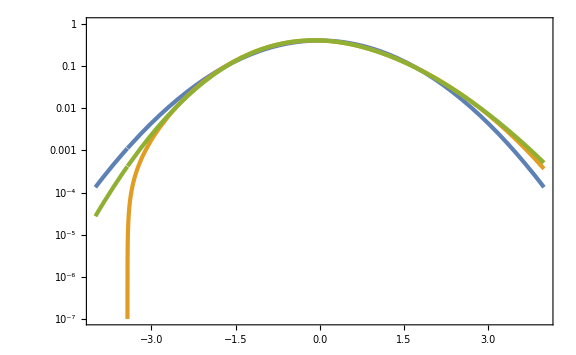

```mathematica
LogPlot[{GaussP[x],EdgeP[x],SkewNP[x]},{x,-4 Pp^(1/2),4 Pp^(1/2)}]
```

## V3

```mathematica
eH[t_]=x'[t]^2/(2 H[t]^2);
```

```mathematica
eta[t_]=eH'[t]/(eH[t]H[t])/.{H'[t]->-eH[t] H[t]^2,x''[t]->-3H[t]x'[t]-V'[x[t]]}//Simplify
```

-6-(2 V'[x[t]])/(H[t] x'[t])+x'[t]^2/H[t]^2

```mathematica
Simplify[Simplify[eta'[t]/H[t]/.{H'[t]->-ϵ[t] H[t]^2,x''[t]->-3H[t]x'[t]-V'[x[t]]}]/.{x'[t]->Sqrt[2ϵ[t]]H[t]},{ϵ[t]>0}]//Expand
```

-12 ϵ[t]+4 ϵ[t]^2-(3 √2 V'[x[t]])/(H[t]^2 √ϵ[t])-(3 √2 √ϵ[t] V'[x[t]])/H[t]^2-V'[x[t]]^2/(H[t]^4 ϵ[t])-(2 V''[x[t]])/H[t]^2

```mathematica
Simplify[Simplify[eta'[t]/H[t]/.{H'[t]->-ϵ[t] H[t]^2,x''[t]->-3H[t]x'[t]-V'[x[t]]}]/.{x'[t]->Sqrt[2ϵ[t]]H[t],V'[x[t]]->-Sqrt[2ϵ[t]]V[x[t]]},{ϵ[t]>0}]/.{H[t]->Sqrt[V[x[t]]/3]}//Expand
```

6 ϵ[t]+4 ϵ[t]^2-(6 V''[x[t]])/V[x[t]]

```mathematica
V[x_]=(λ v^4)/12(x^2(6-4a x+3 x^2))/((1+b x^2)^2)/.{a->1,b->1.435-10^-4,v->Sqrt[0.108],λ->2.97 10^-7};
```

```mathematica
x0=(b-1+Sqrt[(b-1)^2+a^2 b])/(a b)/.{a->1,b->1.435}
```

1.19125

```mathematica
(V'''[x0]/v^3)/V[x0]/.{v->Sqrt[0.108]}
```

43.3896

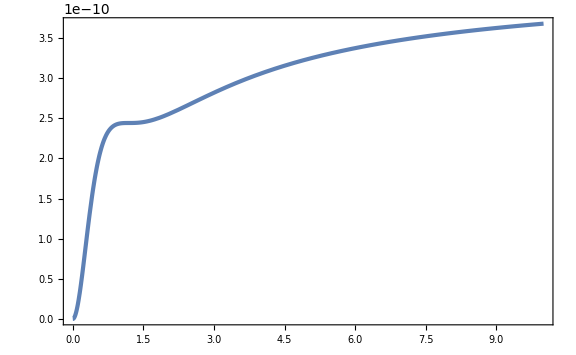

```mathematica
Plot[V[x],{x,0,10}]
```

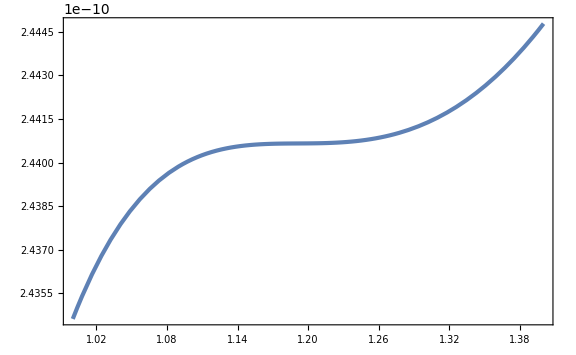

```mathematica
Plot[V[x],{x,1,1.4}]
```

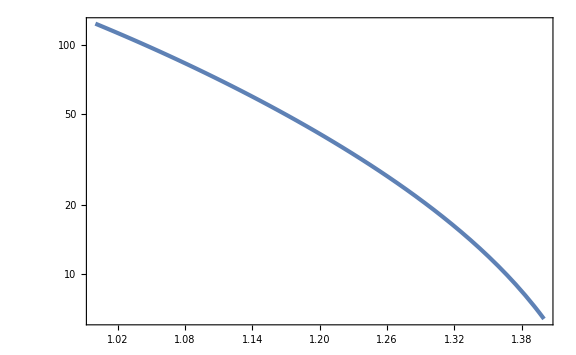

```mathematica
LogPlot[(V'''[x]/v^3)/V[x]/.{v->Sqrt[0.108]},{x,1,1.4}]
```

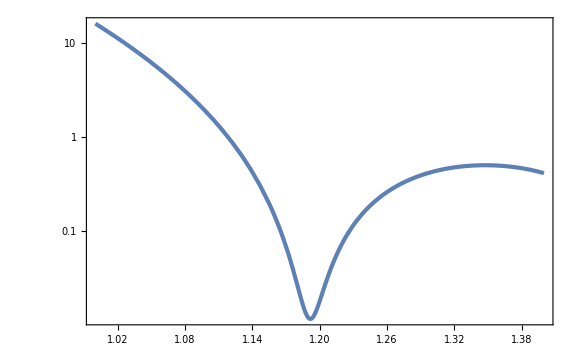

```mathematica
LogPlot[(V'[x]V'''[x]/v^4)/V[x]^2/.{v->Sqrt[0.108]},{x,1,1.4}]
```

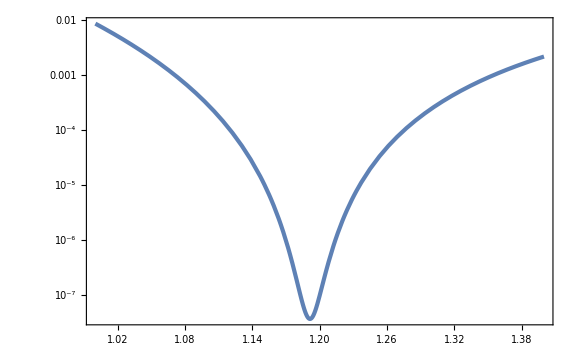

```mathematica
LogPlot[1/2(V'[x]^2/v^2)/V[x]^2/.{v->Sqrt[0.108]},{x,1,1.4}]
```

```mathematica
V[x_]=W0^2/calV^3(cup/calV^(1/3)+aw/(Exp[x/Sqrt[3]]-bw)-cw/Exp[x/Sqrt[3]]+Exp[2x/Sqrt[3]]/calV(dw-gw/(rw Exp[Sqrt[3]x]/calV+1)))/.{aw->0.02,bw->1,cw->0.04,dw->0,gw->3.076278 10^-2,rw->7.071067 10^-1,calV->1000,W0->12.35,cup->0.0382};
```

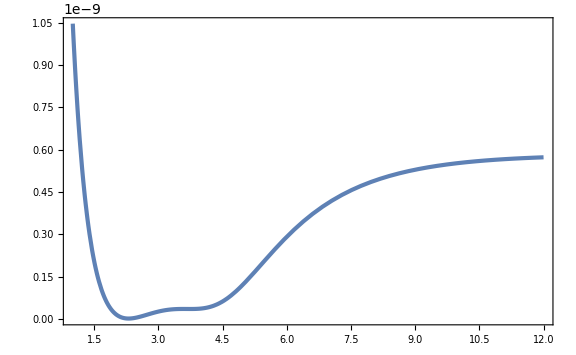

```mathematica
Plot[V[x],{x,1,12}]
```

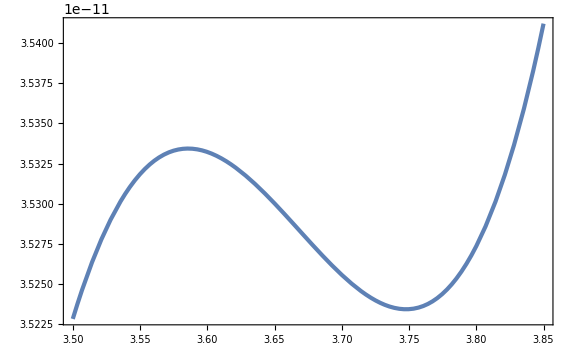

```mathematica
Plot[V[x],{x,3.5,3.85}]
```

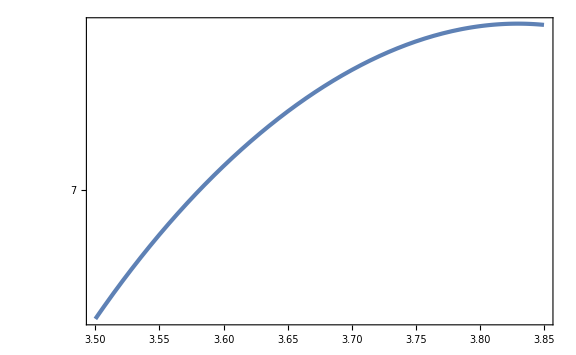

```mathematica
LogPlot[V'''[x]/V[x],{x,3.5,3.85}]
```

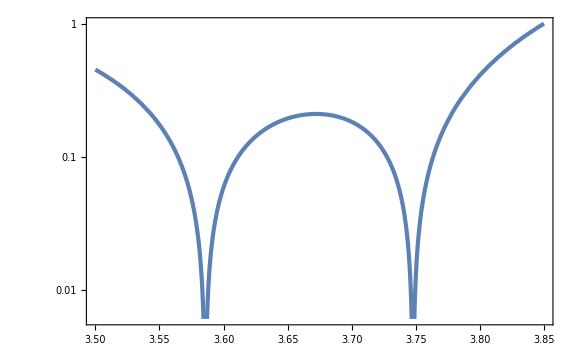

```mathematica
LogPlot[Abs[(V'[x]V'''[x])/V[x]^2],{x,3.5,3.85}]
```

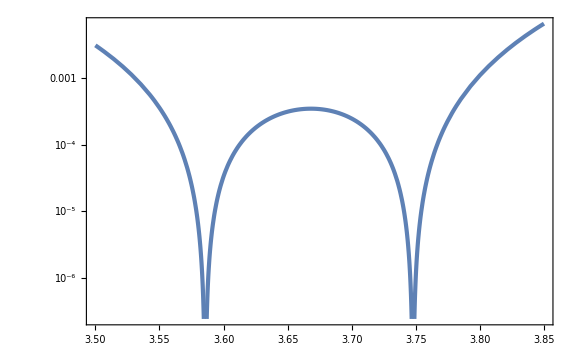

```mathematica
LogPlot[1/2 V'[x]^2/V[x]^2,{x,3.5,3.85}]
```